Philippe Morel
UCL Bartlett
2019-2020

“Colored segments”

Write functions (choose any method and strategy you want) to create a graph like the one below.
I assume that you probably won’t reach the final step. If so, this is not a problem.
Try to go as far as possible

Deadline for file sending: January 7th, 2020, at 6pm London time

```mathematica
(* Reminder: always clear everything before starting to work on a new set of functions *)

ClearAll["Global`*"];
```

## Step1: Create Random Points

```mathematica
xyzCoordinates:={RandomReal[{1,200}],RandomReal[{1,200}]};
myPointList=Table[xyzCoordinates,200];
```

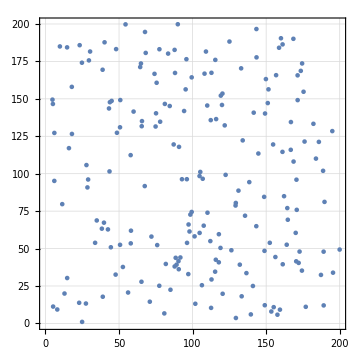

```mathematica
Show[ListPlot[Table[xyzCoordinates,200]],Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

## Step2: Create Line

```mathematica
Partition[myPointList,2];
```

```mathematica
myLine=Line[#]&/@Partition[myPointList,2];
```

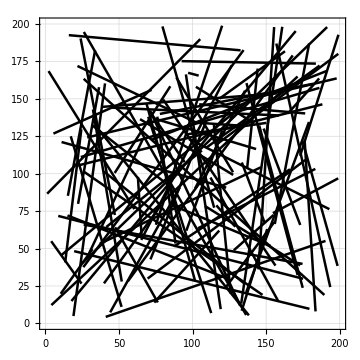

```mathematica
Graphics[{Thickness[0.005],myLine},Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

## Step3: Find Intersection

### Firstly, we need to find the lines intersected with line y=100

### Extract y value:

```mathematica
myPointList;
```

```mathematica
yValue=Flatten[Take[Flatten[myPointList],{2,-1,2}]];
```

### test whether two points is on the different sides of line.

```mathematica
testValue=Partition[yValue,2]-100;
```

```mathematica
Y[x_]:=Take[Flatten[testValue],{x,-1,2}]
```

```mathematica
Y[1]
```

{22.5521,98.866,-26.3645,26.7856,92.8154,-0.814655,64.904,-48.2718,3.20809,-90.4621,-86.0016,-9.32749,2.95117,72.2171,-20.1452,-14.7785,-9.30272,7.4743,-61.3827,-94.6067,42.926,32.5148,-22.7081,33.9382,-62.4292,68.5308,-88.2483,22.4753,40.2154,30.1546,92.5352,67.3937,-95.6422,46.3385,-86.8101,75.1828,-5.62113,-80.9963,-61.5976,-27.5649,-21.0441,32.1814,-54.6017,-23.683,-27.5767,-45.0836,39.931,3.59397,-35.418,19.3812,64.297,-71.9061,57.3255,-28.1998,-44.2205,-2.56419,-9.95388,24.9892,-46.798,-33.5884,81.7857,38.9163,-53.1269,33.9182,58.0568,-59.5254,-38.0771,-50.3777,46.3683,44.0306,-95.0897,89.8758,-57.2337,-34.0023,29.6471,97.9531,58.4084,-21.5905,44.6337,95.2776,-32.4402,24.216,-93.1068,31.9211,86.9541,34.5272,-80.9732,60.5189,-51.7254,-71.5911,-73.6932,36.8432,15.4723,38.0841,-37.0619,-37.9986,9.18335,-69.7974,-94.3846,-40.9632}

```mathematica
Y[2]
```

{68.7065,-34.1298,-3.10723,55.9852,11.9545,36.4244,-87.7624,-20.7119,-36.4429,66.3227,-35.7857,21.1491,-48.5662,17.3241,57.789,82.3741,-92.6176,-32.668,49.5673,32.9643,-72.0401,-80.1346,98.3748,26.3075,82.591,-23.6691,41.8398,-91.9763,63.6232,-34.2644,82.4086,65.5093,-44.8957,5.48573,98.1277,73.5371,32.0579,63.3911,21.4639,-51.1469,-73.2512,-76.2375,49.7973,23.225,90.3375,-73.3938,60.0115,70.1993,-21.135,80.0524,0.952876,79.0096,11.1229,-70.1723,72.3572,-85.142,55.4392,-88.9512,4.29333,87.0163,50.1753,44.1531,23.6201,71.9464,33.6242,97.9441,28.7618,-80.209,40.2574,7.734,60.318,-13.3622,35.3078,-60.2314,-59.2437,-63.9498,0.485198,-61.2309,53.6291,-85.0509,-76.2284,63.6582,38.0515,34.3222,-75.7343,-79.0998,1.47137,-67.7364,-90.263,46.7436,1.42964,16.4743,-35.5932,-46.6241,-91.5562,-86.0358,-70.046,-27.904,94.6552,-2.15818}

```mathematica
Y[1]*Y[2]
```

{1549.48,-3374.27,81.9207,1499.6,1109.56,-29.6733,-5696.13,999.803,-116.912,-5999.69,3077.63,-197.268,-143.327,1251.1,-1164.17,-1217.36,861.596,-244.17,-3042.57,-3118.64,-3092.39,-2605.56,-2233.9,892.829,-5156.09,-1622.06,-3692.29,-2067.19,2558.63,-1033.23,7625.69,4414.91,4293.93,254.2,-8518.48,5528.73,-180.202,-5134.44,-1322.12,1409.86,1541.5,-2453.43,-2719.02,-550.039,-2491.21,3308.86,2396.32,252.294,748.56,1551.51,61.2671,-5681.27,637.627,1978.84,-3199.67,218.321,-551.835,-2222.82,-200.919,-2922.74,4103.62,1718.27,-1254.86,2440.29,1952.11,-5830.16,-1095.17,4040.74,1866.66,340.532,-5735.62,-1200.94,-2020.8,2048.,-1756.41,-6264.08,28.3396,1322.,2393.66,-8103.45,2472.87,1541.55,-3542.85,1095.6,-6585.41,-2731.09,-119.142,-4099.33,4668.89,-3346.42,-105.355,606.965,-550.71,-1775.64,3393.25,3269.24,-643.257,1947.63,-8933.99,88.4061}

```mathematica
YY[x_]:=Take[Flatten[Y[1]*Y[2]],{x}]
```

```mathematica
YY[1]
```

{1549.48}

```mathematica
Sign[YY[1]]
```

{1}

```mathematica
Table[Sign[YY[x]],{x,100}]
```

{{1},{-1},{1},{1},{1},{-1},{-1},{1},{-1},{-1},{1},{-1},{-1},{1},{-1},{-1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{-1},{-1},{-1},{-1},{1},{-1},{1},{1},{1},{1},{-1},{1},{-1},{-1},{-1},{1},{1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{1},{1},{-1},{1},{1},{-1},{1},{-1},{-1},{-1},{-1},{1},{1},{-1},{1},{1},{-1},{-1},{1},{1},{1},{-1},{-1},{-1},{1},{-1},{-1},{1},{1},{1},{-1},{1},{1},{-1},{1},{-1},{-1},{-1},{-1},{1},{-1},{-1},{1},{-1},{-1},{1},{1},{-1},{1},{-1},{1}}

```mathematica
linePosition=Flatten[Position[Table[Sign[YY[x]],{x,100}],{-1}]]
```

{2,6,7,9,10,12,13,15,16,18,19,20,21,22,23,25,26,27,28,30,35,37,38,39,42,43,44,45,52,55,57,58,59,60,63,66,67,71,72,73,75,76,80,83,85,86,87,88,90,91,93,94,97,99}

```mathematica
Length[linePosition]
```

54

```mathematica
intersectedLine=Part[myLine,linePosition];
```

```mathematica
pointsOFintersectedLine=intersectedLine/.(Line[{a_,b_}])->{a,b};
```

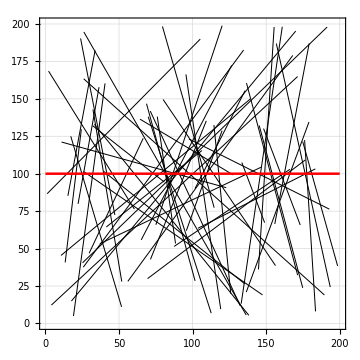

```mathematica
Graphics[{Thickness[0.002],intersectedLine,Red,Thickness[0.005],Line[{{0,100},{200,100}}]},Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

## Step4: Divide lines by Intersection

### We need to find intersection. In order to that, we need to use the knowledge of matrix. Firstly, we know that the data of a line is a 2x2 matrix.

```mathematica
intersectedLine[[1]]
```

Line[{{120.066,198.866},{75.0314,65.8702}}]

```mathematica
pointsOFintersectedLine[[1]]
```

{{120.066,198.866},{75.0314,65.8702}}

### we can define Two lines, L_1 containing the points a and b with line L_2 containing the points c and d

```mathematica
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
```

### for L2 y=100, we can define it with (0,100),(200,100)

```mathematica
myIntersection[{a_,b_}]:=(Det[{a,b}]{-200,0}-Det[{{0,100},{200,100}}](a-b))/Det[{a-b,{-200,0}}]
```

```mathematica
myIntersection[{{1,0},{2,2}}]
```

{51,100}

```mathematica
myIntersection[pointsOFintersectedLine[[1]]]
```

{86.5884,100.}

```mathematica
allIntersectedPoints=Table[myIntersection[pointsOFintersectedLine[[x]]],{x,Length[linePosition]}]
```

{{86.5884,100.},{126.214,100.},{100.22,100.},{176.979,100.},{105.464,100.},{88.5981,100.},{161.681,100.},{25.8349,100.},{18.0416,100.},{136.336,100.},{114.088,100.},{60.3847,100.},{39.5743,100.},{117.796,100.},{108.08,100.},{72.6166,100.},{45.4548,100.},{90.8784,100.},{177.598,100.},{159.919,100.},{146.133,100.},{73.5585,100.},{97.7974,100.},{180.979,100.},{154.067,100.},{77.7922,100.},{144.737,100.},{41.7138,100.},{109.396,100.},{88.3992,100.},{106.819,100.},{24.7625,100.},{137.231,100.},{162.371,100.},{55.1145,100.},{88.0407,100.},{109.576,100.},{32.1511,100.},{14.6053,100.},{94.8336,100.},{20.701,100.},{148.978,100.},{89.5464,100.},{82.2573,100.},{176.507,100.},{166.144,100.},{28.093,100.},{153.038,100.},{81.7192,100.},{41.5426,100.},{86.6225,100.},{81.5769,100.},{164.192,100.},{81.3375,100.}}

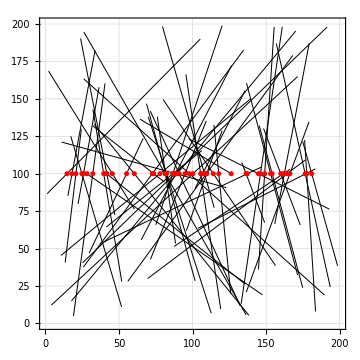

```mathematica
Graphics[{Thickness[0.002],intersectedLine,Red,PointSize[0.01],Point[allIntersectedPoints]},Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

## Step 5 graph lines

### divide all intersected lines into 2 lines.

```mathematica
interSection[x_]:=myIntersection[pointsOFintersectedLine[[x]]]
```

```mathematica
pointsOFintersectedLine[[1]]
```

{{120.066,198.866},{75.0314,65.8702}}

```mathematica
pointsOFintersectedLine[[1]][[1]]
```

{120.066,198.866}

```mathematica
interSection[1]
```

{86.5884,100.}

```mathematica
Line[{pointsOFintersectedLine[[1]][[1]],interSection[1]}]
```

Line[{{120.066,198.866},{86.5884,100.}}]

```mathematica
Line[{pointsOFintersectedLine[[1]][[2]],interSection[1]}]
```

Line[{{75.0314,65.8702},{86.5884,100.}}]

```mathematica
Line[{pointsOFintersectedLine[[2]][[1]],interSection[2]}]
```

Line[{{127.599,99.1853},{126.214,100.}}]

```mathematica
newLine1[x_]:=Line[{pointsOFintersectedLine[[x]][[1]],interSection[x]}]
```

```mathematica
newLine1[1]
```

Line[{{120.066,198.866},{86.5884,100.}}]

```mathematica
newLine2[x_]:=Line[{pointsOFintersectedLine[[x]][[2]],interSection[x]}]
```

```mathematica
allLine1=Table[newLine1[x],{x,Length[linePosition]}];
```

```mathematica
allLine2=Table[newLine2[x],{x,Length[linePosition]}];
```

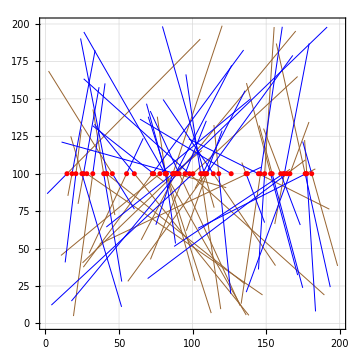

```mathematica
Graphics[{Thickness[0.002],Brown,allLine1,Thickness[0.002],Blue,allLine2,Red,PointSize[0.01],Point[allIntersectedPoints]},Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

```mathematica
nolinePosition=Flatten[Position[Table[Sign[YY[x]],{x,100}],{1}]]
```

{1,3,4,5,8,11,14,17,24,29,31,32,33,34,36,40,41,46,47,48,49,50,51,53,54,56,61,62,64,65,68,69,70,74,77,78,79,81,82,84,89,92,95,96,98,100}

```mathematica
nointersectedLine=Part[myLine,nolinePosition];
```

```mathematica
allSegments=Join[allLine1,allLine2,nointersectedLine];
```

```mathematica
Length[allSegments]
```

154

### Now we need to color all segments

```mathematica
allEndPoints=allSegments/.(Line[{a_,b_}])->{a,b};
```

```mathematica
yValueOfAllEndPoints=Flatten[Take[Flatten[allEndPoints],{2,-1,2}]];
```

```mathematica
Sign[Round[yValueOfAllEndPoints-100,0.01]];
```

```mathematica
Partition[Sign[Round[yValueOfAllEndPoints-100,0.01]],2]
```

{{1,0},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{1,0},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{1,0},{-1,0},{1,0},{1,0},{1,0},{-1,0},{1,0},{1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{1,0},{1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{1,0},{-1,0},{1,0},{1,0},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{1,0},{1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{1,0},{1,0},{1,0},{-1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{-1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{-1,0},{1,0},{-1,0},{-1,0},{-1,0},{1,0},{-1,0},{-1,0},{1,0},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{-1,0},{1,0},{1,1},{-1,-1},{1,1},{1,1},{-1,-1},{-1,-1},{1,1},{-1,-1},{1,1},{1,1},{1,1},{1,1},{-1,-1},{1,1},{1,1},{-1,-1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{1,1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{1,1},{1,1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{1,1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{-1,-1},{-1,-1},{-1,-1}}

```mathematica
Total[Partition[Sign[Round[yValueOfAllEndPoints-100,0.01]],2],{2}];
```

```mathematica
finalValue=Sign[Total[Partition[Sign[Round[yValueOfAllEndPoints-100,0.01]],2],{2}]];
```

```mathematica
upPosition=Flatten[Position[finalValue,1]];
```

```mathematica
lowPosition=Flatten[Position[finalValue,-1]];
```

```mathematica
upperLines=Part[allSegments,upPosition];
```

```mathematica
lowLines=Part[allSegments,lowPosition];
```

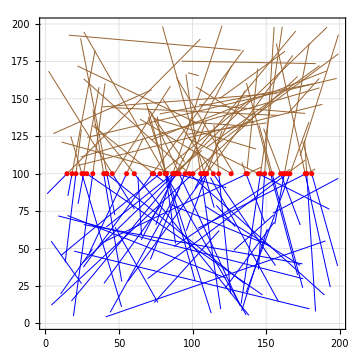

```mathematica
Graphics[{Thickness[0.002],Brown,upperLines,Thickness[0.002],Blue,lowLines,Red,PointSize[0.01],Point[allIntersectedPoints]},Frame->True,PlotRange->{{0,200},{0,200}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

## Finish!!